```mathematica
<<xlr8r.m
```

xlr8r 0.60 (15-Oct-2007) loaded 15-October-2007 14:45:30.406387 using Mathematica 6.0 for Mac OS X x86 (32-bit) (June 19, 2007)

xCellerator implementaton
Created: 12 August 2005 BES
Revised: 15 Oct 2007 BES Test under Mathematica Version 6.0

## Field-Noyes Model of Belousov-Zhabotinski Reaction

Standard Abbreviations:
	X=HBrO_2 (HBrO in model below)
	Y=Br^+ (Br in model below)
	Z=Ce^(4+)(Ce in model below)
	A = BrO_3^-(BrO3 in model below)
	P = HOBr

References
R.J.Field and R.M.Noyes,J.Chem.Phys.60,1877 (1974); 
R.J.Field,E.Koros,R.M.Noyes,JACS 94,8649 (1972);
R.J.Field,R.M.Noyes,Nature 237,390 (1972) 

This implementation is taken from J.D. Murray, "Mathematical Biology" (1989) page 181.

```mathematica
FNModel= {{BrO3+Br->HBrO2+HOBr, k1 },{HBrO2+Br->2HOBr, k2},
{BrO3+HBrO2->2 HBrO2 +2  Ce, k3  },{2 HBrO2->BrO3 + HOBr, k4},  {Ce->.5 Br,  k5}}
```

{{Br+BrO3→HBrO2+HOBr,k1},{Br+HBrO2→2 HOBr,k2},{BrO3+HBrO2→2 Ce+2 HBrO2,k3},{2 HBrO2→BrO3+HOBr,k4},{Ce→0.5 Br,k5}}

```mathematica
interpret[FNModel,frozen-> BrO3][[1]]//TableForm
```

Br'[t]==-k1 Br[t] BrO3[t]+0.5 k5 Ce[t]-k2 Br[t] HBrO2[t]
BrO3'[t]==0
Ce'[t]==-k5 Ce[t]+2 k3 BrO3[t] HBrO2[t]
HBrO2'[t]==k1 Br[t] BrO3[t]-k2 Br[t] HBrO2[t]+k3 BrO3[t] HBrO2[t]-2 k4 HBrO2[t]^2
HOBr'[t]==k1 Br[t] BrO3[t]+2 k2 Br[t] HBrO2[t]+k4 HBrO2[t]^2

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {HOBr}

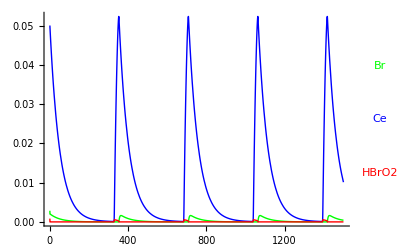

```mathematica
ics={HBrO2-> .001, Br->.003, Ce->.05,BrO3-> .1};
r={k1-> 1.3, k2-> 2*10^6, k3-> 34, k4-> 3*10^3, k5-> 0.02, BrO3[t]->.1};
sys=interpret[FNModel,frozen-> {BrO3}]; 
s=run[sys,
timeSpan-> 1500,
rates-> r, 
initialConditions-> ics];
runPlot[s, {Br, Ce, HBrO2}, PlotRange-> All]
```

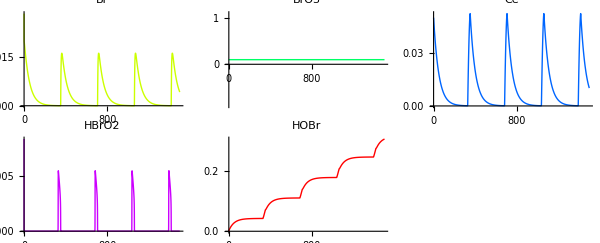

```mathematica
gridPlot[s, ImageSize-> 600]
```